```mathematica
ClearAll["Global`*"]
```

```mathematica
Mpl=1.0;                    (* reduced mass Planck *)
mϕ=1.0;                      (* inflation mass *)
λ=0.0;(*0.05;*)                      (* self-coupling constant *)
g=200.0;(*10.0;*)                      (* coupling constant ϕ-χ *)
k=1.0;                        (* comoving momentum for χ *)
tMax=50.0;            (* Time *)
Φ=0.1 Mpl;                     (* Initial amplitude ϕ *)
```

## Daughter dynamic:

```mathematica
(* Frequency *)
ω2[t_]:=k^2+g^2 Φ^2 Sin[mϕ t]^2;
ω[t_]:=√ω2[t];

(* EOM daughter χ *)
eqχ=χ''[t]+ω2[t]*χ[t]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0])),χ'[0]==-I*√(ω[0]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=NDSolve[{eqχ,χconditions[[1]],χconditions[[2]]},χ,{t,0,tMax},MaxSteps->Infinity,Method->"StiffnessSwitching"];

(* Solution χ *)
χsol[t_]:=Evaluate[χ[t]/. solχ[[1]]];

(* Number particles *)
numbχ[t_]:=1/2 Abs[χ'[t]]^2/ω[t]+ω[t]/2 Abs[χ[t]]^2-1/2
numbχsol[t_]:=Evaluate[numbχ[t]/. solχ[[1]]];
```

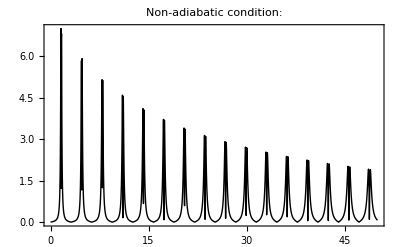

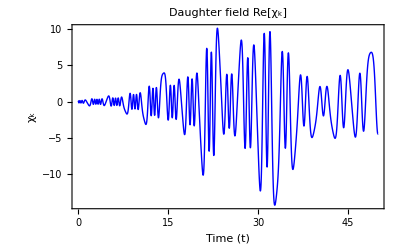

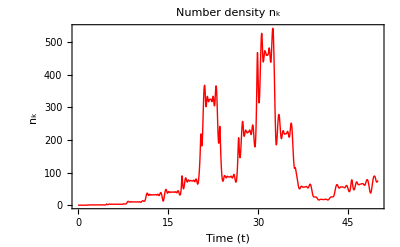

```mathematica
(*Plots *)
Plot[ Abs[ω'[t]]/ω2[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Black},Frame->True,PlotLabel->"Non-adiabatic condition:  "]
Plot[Re[χsol[t]],{t,0,tMax},PlotRange->All,PlotStyle->{Thick ,Blue},Frame->True,FrameLabel->{"Time (t)","χ_k"},PlotLabel->"Daughter field Re[χ_k]"]
Plot[numbχsol[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"Time (t)","n_k"},PlotLabel->"Number density n_k"]
```

## Check equivalence with Mathieu equation: ,

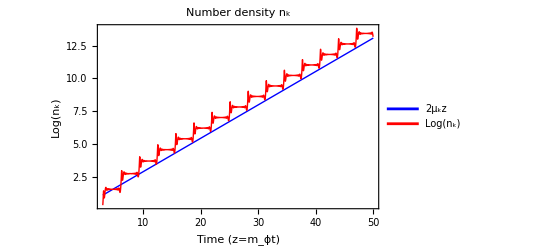

```mathematica
(* Map to Mathieu equation *)
q = (g^2 Φ^2)/(4 mϕ^2);
A = k^2/mϕ^2+2q;

(* Mathieu equation for the daughter field *)
eqχMathieu = χnew''[z] + (A - 2q Cos[2 z])χnew[z]==0;

(* Solve it *)
solχMathieu = NDSolve[{eqχMathieu,χnew[0]==1/(√(2 √(A - 2 q Cos[0]))),χnew'[0]==-I*√((√(A - 2 q Cos[0]))/2)},χnew,{z,0, mϕ*tMax},MaxSteps->Infinity,Method->"StiffnessSwitching"];

χnewsol[z_]:=Evaluate[χnew[z]/.solχMathieu[[1]]];

(* Number particles *)
numbχnewsol[z_]:=1/2 Abs[χnewsol'[z]]^2/(√(A - 2 q Cos[2 z]))+(√(A - 2 q Cos[2 z]))/2 Abs[χnewsol[z]]^2-1/2
y= 2*Abs[Im[MathieuCharacteristicExponent[A,q]]]*z;
(* Plot *)
μplot = Plot[y+ Log[numbχnewsol[3]],{z,3,tMax},PlotRange->All,PlotStyle->{Thick,Blue},PlotLegends->{"2μ_kz"},Frame->True];
nplot = Plot[Log[numbχnewsol[z]],{z,3,tMax},PlotRange->All,PlotStyle->{Thick,Red},PlotLegends->{"Log(n_k)"},Frame->True];
Show[μplot,nplot,FrameLabel->{"Time (z=m_ϕt)","Log(n_k)"},PlotLabel->"Number density n_k"]
```

## Stability / Instability chart

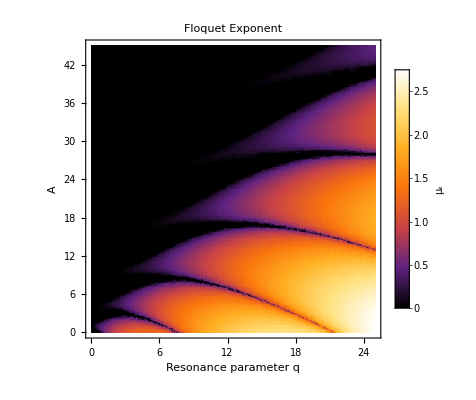

```mathematica
qMaxChart=25;
AMaxChart=45;

μ[A_,q_]:=Abs[Im[MathieuCharacteristicExponent[A,q]]];

plotFloquet=DensityPlot[μ[A,q],{q,0,qMaxChart},{A,0,AMaxChart},PlotPoints->80,MaxRecursion->2,ColorFunction->"SunsetColors",PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"μ_k"],FrameLabel->{"Resonance parameter q","A"},PlotLabel->"Floquet Exponent"]
```

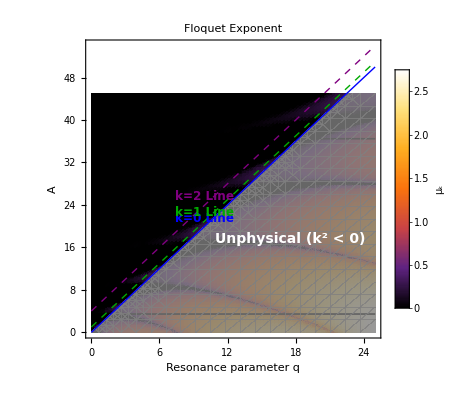

```mathematica
unphysicalRegion=RegionPlot[A<2*q,{q,0,qMaxChart},{A,0,AMaxChart},BoundaryStyle->None,PlotStyle->Directive[Gray,Opacity[0.8]]];

nBands=10;
bands=Flatten[Table[{MathieuCharacteristicB[n,q],MathieuCharacteristicA[n,q]},{n,1,nBands}]];
plotBands=Plot[Evaluate[bands],{q,0,qMaxChart},PlotStyle->Directive[Black,Thin],PlotRange->{{0,qMaxChart},{0,AMaxChart}}];

lineK[k_,q_]:= k^2/mϕ^2+2q;

plotKLines=Plot[{lineK[0.0,q],lineK[1.0,q],lineK[2.0,q]},{q,0,qMaxChart},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Darker[Green],Dashed],Directive[Thick,Purple,Dashed]}];

plotMathieuCombined=Show[plotFloquet,plotBands,unphysicalRegion,plotKLines,Epilog->{Text[Style["Unphysical (k^2 < 0)",White,Bold,14],{qMaxChart*0.7,qMaxChart*0.7}],Text[Style["k=0 Line",Blue,Bold,12],{qMaxChart*0.4,lineK[0.0,qMaxChart*0.4]+1.5}],Text[Style["k=1 Line",Darker[Green],Bold,12],{qMaxChart*0.4,lineK[1.0,qMaxChart*0.4]+1.5}],Text[Style["k=2 Line",Purple,Bold,12],{qMaxChart*0.4,lineK[2.0,qMaxChart*0.4]+1.5}]}]
```